```mathematica
CalibrationHg=Import["/Users/alex/Library/Mobile Documents/com~apple~CloudDocs/Лабы/Labs/Phys_Labs/5_sem/Exam lab/Calibration_Hg.xlsx"][[1]][[2;;All,1;;2]];
```

```mathematica
calibWaveLengths=CalibrationHg[[All,1]];
calibPixel=CalibrationHg[[All,2]];
calibrationHgReady=Transpose[ArrayReshape[AppendTo[calibPixel,calibWaveLengths],{2,Length[calibWaveLengths]}]];
```

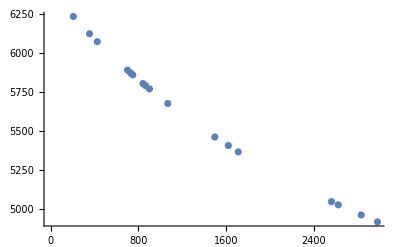

```mathematica
ListPlot[calibrationHgReady]
```

```mathematica
fit=FindFit[calibrationHgReady,{a+c/(x-b),b<0},{a,b,c},x]
```

{a→2889.97,b→-4060.89,c→1.42866×10^7}

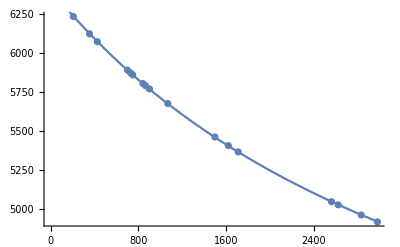

```mathematica
Show[ListPlot[calibrationHgReady],Plot[a+c/(x-b)/.fit,{x,0,3000}]]
```

```mathematica
lampImage=Import["/Users/alex/Library/Mobile Documents/com~apple~CloudDocs/Лабы/Labs/Phys_Labs/5_sem/Exam lab/26_11_2018/lamp.jpeg"]
```

-Graphics-

```mathematica
lampSpectre=ReadList["/Users/alex/Library/Mobile Documents/com~apple~CloudDocs/Лабы/Labs/Phys_Labs/5_sem/Exam lab/26_11_2018/lamp2.txt",Number,WordSeparators->{"\t", "\n"}]
```

{0.,608.222,617.055,617.807,623.458,0.1,610.632,617.034,618.729,623.434,0.2,627.68,617.019,619.186,150327,600.772,617.161,617.417,623.654,3006.9,600.766,617.122,617.455,623.572,3007.,600.759,617.086,617.618,623.497}
 |  |  |  |

```mathematica
lampSpectre=ArrayReshape[lampSpectre,{Length[lampSpectre]/5,5}]
```

{{0.,608.222,617.055,617.807,623.458},{0.1,610.632,617.034,618.729,623.434},{0.2,627.68,617.019,619.186,623.415},30066,{3006.9,600.766,617.122,617.455,623.572},{3007.,600.759,617.086,617.618,623.497}}
 |  |  |  |